# Information FFL C3

```mathematica
Subscript[K, px]=200 ; (*Tasa de sintesis de proteina X*)
Subscript[K, py]=300;  (*Tasa de sintesis de proteina Y*)
Subscript[K, pz]=100 ; (*Tasa de sintesis de proteina Z*)

Hill=2 ;

Subscript[γ, x]=1/5;      (*Tasa de degradación de ARNmX*)
Subscript[γ, y]=1/7 ;      (*Tasa de degradación de ARNmY*)
Subscript[γ, z]=1/10 ;     (*Tasa de degradación de ARNmZ*)

Subscript[μ, x]=1/20 ;   (*Tasa de degradación de proteina X*)
Subscript[μ, y]=1/40;    (*Tasa de degradación de proteina Y*)
Subscript[μ, z]=1/30 ;   (*Tasa de degradación de proteina Z*)

Subscript[M, x] = Subscript[K, x]/Subscript[γ, x];     (*Valor estado estacionario de ARNm X*)
X=Subscript[K, px]/Subscript[μ, x] Subscript[M, x];  (*Valor estado estacionario de proteina X*)

Subscript[M, y] = 10;
Subscript[M, z] = 25;

Y = Subscript[K, py]/Subscript[μ, y] Subscript[M, y];

Z = N[Subscript[K, pz]/Subscript[μ, z] Subscript[M, z]];

Subscript[K, xy]=X;
Subscript[K, xz]=X;
Subscript[K, yz]=2Y;

Subscript[K, y]=N[Subscript[M, y] Subscript[γ, y]((X^Hill+Subscript[K, xy]^Hill)/X^Hill)];

Subscript[K, z]=Subscript[M, z] Subscript[γ, z](((Y^Hill+Subscript[K, yz]^Hill)(X^Hill+Subscript[K, xz]^Hill))/(Subscript[K, xz]^Hill Subscript[K, yz]^Hill));

FuncionHillY[X_]:=Subscript[K, y] X^Hill/(X^Hill+Subscript[K, xy]^Hill);

FuncionHillZ[Y_, X_]:=Subscript[K, z](Subscript[K, yz]^Hill     Subscript[K, xz]^Hill)/((Y^Hill+Subscript[K, yz]^Hill)(X^Hill+Subscript[K, xz]^Hill));

DerivadaFuncionHillYX[X_]:=Subscript[K, y](Hill Subscript[K, xy]^Hill X^(Hill-1))/((X^Hill + Subscript[K, xy]^Hill)^2);

DerivadaFuncionHillZX[X_,Y_]:=-Subscript[K, z](Subscript[K, yz]^Hill Hill  Subscript[K, xz]^Hill  X^(Hill-1))/((Y^Hill+Subscript[K, yz]^Hill)(X^Hill+Subscript[K, xz]^Hill)^2);

DerivadaFuncionHillZY[X_,Y_]:=-Subscript[K, z](Subscript[K, xz]^Hill Hill Subscript[K, yz]^Hill Y^(Hill-1))/((X^Hill+Subscript[K, xz]^Hill)(Y^Hill+Subscript[K, yz]^Hill)^2);


Jaccobiano2 = Refine[{{-Subscript[γ, x],0,0,0,0,0}, {0,-Subscript[γ, y],0,DerivadaFuncionHillYX[X],0,0}, {0,0,-Subscript[γ, z],DerivadaFuncionHillZX[X,Y],DerivadaFuncionHillZY[X,Y],0}, {Subscript[K, px],0,0,-Subscript[μ, x],0,0}, {0,Subscript[K, py],0,0,-Subscript[μ, y],0}, {0,0,Subscript[K, pz],0,0,-Subscript[μ, z]}}, Assumptions ->{ Subscript[γ, x]>0,Subscript[γ, y]>0,Subscript[γ, z]>0, Subscript[μ, x]>0, Subscript[μ, y]>0 , Subscript[μ, z]>0, Subscript[K, px] >0, Subscript[K, py]>0, Subscript[K, pz]>0,Element[Subscript[γ, x],Reals], Element[Subscript[γ, y],Reals], Element[Subscript[γ, z],Reals], Element[Subscript[μ, x],Reals], Element[Subscript[μ, y],Reals], Element[Subscript[μ, z],Reals],Element[Subscript[K, px],Reals],Element[Subscript[K, py],Reals],Element[Subscript[K, pz],Reals]}];

Difusion2 =- {{Subscript[δ, mx]}, {Subscript[δ, my]}, {Subscript[δ, mz]}, {Subscript[δ, x]}, {Subscript[δ, y]}, {Subscript[δ, z]}}. {{Subscript[δ, mx]}, {Subscript[δ, my]}, {Subscript[δ, mz]}, {Subscript[δ, x]}, {Subscript[δ, y]}, {Subscript[δ, z]}}ᵀ /.{ Subscript[δ, mx] Subscript[δ, my]-> 0,Subscript[δ, mx] Subscript[δ, mz]-> 0,Subscript[δ, mx] Subscript[δ, x]-> 0,Subscript[δ, mx] Subscript[δ, y]-> 0,Subscript[δ, mx] Subscript[δ, z]-> 0, Subscript[δ, my] Subscript[δ, mz]-> 0,Subscript[δ, my] Subscript[δ, x]-> 0,Subscript[δ, my] Subscript[δ, y]-> 0,Subscript[δ, my] Subscript[δ, z]-> 0, Subscript[δ, mz] Subscript[δ, x]-> 0,Subscript[δ, mz] Subscript[δ, y]-> 0,Subscript[δ, mz] Subscript[δ, z]-> 0, Subscript[δ, x] Subscript[δ, y]-> 0,Subscript[δ, x] Subscript[δ, z]-> 0, Subscript[δ, y] Subscript[δ, z]-> 0, Subscript[δ, mx] Subscript[δ, mx]-> 2 Subscript[γ, x] Subscript[M, x], Subscript[δ, my] Subscript[δ, my]-> 2 Subscript[γ, y] Subscript[M, y], Subscript[δ, mz] Subscript[δ, mz]-> 2 Subscript[γ, z] Subscript[M, z], Subscript[δ, x] Subscript[δ, x]-> 2 Subscript[μ, x] X, Subscript[δ, y] Subscript[δ, y]-> 2 Subscript[μ, y] Y, Subscript[δ, z] Subscript[δ, z]-> 2 Subscript[μ, z] Z };
```

```mathematica
MatricesCovarianzas = Table[LyapunovSolve[Jaccobiano2, Difusion2],{Subscript[K, x],50}];
```

```mathematica
valorEsperadoX = Table[Subscript[K, px]/Subscript[μ, x] Subscript[K, x]/Subscript[γ, x] , {Subscript[K, x],50}];

valorEsperadoY = Table[Subscript[K, py]/Subscript[μ, y] Subscript[M, y], {Subscript[K, x],50}];

valorEsperadoZZ = Table[Subscript[K, pz]/Subscript[μ, z] Subscript[M, z], {Subscript[K, x],50}];

RuidoYX = Table[(MatricesCovarianzas[[indice]][[4,5]])/(valorEsperadoX[[indice]]valorEsperadoY[[indice]]),{indice,50}];

RuidoZX = Table[(MatricesCovarianzas[[indice]][[4,6]])/(valorEsperadoX[[indice]]*valorEsperadoZZ[[indice]]),{indice,50}];

RuidoZY =  Table[(MatricesCovarianzas[[indice]][[5,6]])/(valorEsperadoY[[indice]]*valorEsperadoZZ[[indice]]),{indice,50}];
```

```mathematica
RuidoFFLC3 = {RuidoYX,RuidoZX, RuidoZY };

Export["Ruido_FFL_C3_Hill2.csv",RuidoFFLC3,"CSV"]
```

Ruido_FFL_C3_Hill2.csv

```mathematica
InformacionYXvariante = Table[1/2 Log[2,(MatricesCovarianzas[[indice]][[5,5]]*MatricesCovarianzas[[indice]][[4,4]])/(MatricesCovarianzas[[indice]][[5,5]]*MatricesCovarianzas[[indice]][[4,4]] -(MatricesCovarianzas[[indice]][[5,4]])^2 )], {indice,50}];

InformacionZXvariante = Table[1/2 Log[2,(MatricesCovarianzas[[indice]][[6,6]]*MatricesCovarianzas[[indice]][[4,4]])/(MatricesCovarianzas[[indice]][[6,6]]*MatricesCovarianzas[[indice]][[4,4]] -(MatricesCovarianzas[[indice]][[6,4]])^2 )], {indice,50}];

InformacionZYvariante = Table[1/2 Log[2,(MatricesCovarianzas[[indice]][[6,6]]*MatricesCovarianzas[[indice]][[5,5]])/(MatricesCovarianzas[[indice]][[6,6]]*MatricesCovarianzas[[indice]][[5,5]] -(MatricesCovarianzas[[indice]][[6,5]])^2 )], {indice,50}];

InformacionZXYvariante = Table[1/2 Log[2,(MatricesCovarianzas[[indice]][[6,6]]*MatricesCovarianzas[[indice]][[5,5]]*MatricesCovarianzas[[indice]][[4,4]]-(MatricesCovarianzas[[indice]][[5,4]])^2)/Det[MatricesCovarianzas[[indice]][[4;;6,4;;6]]]], {indice,50}];
```

```mathematica
informacionFFLC3 = {InformacionYXvariante,InformacionZXvariante, InformacionZYvariante, InformacionZXYvariante };

Export["datos_FFL_C3_Hill1.csv",informacionFFLC3,"CSV"]
```

datos_FFL_C3_Hill1.csv

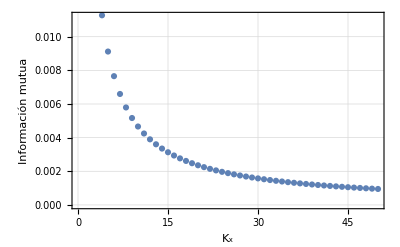

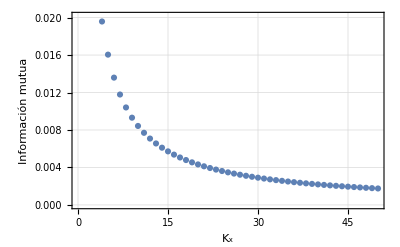

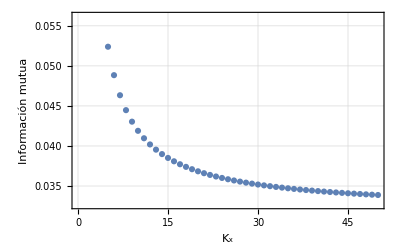

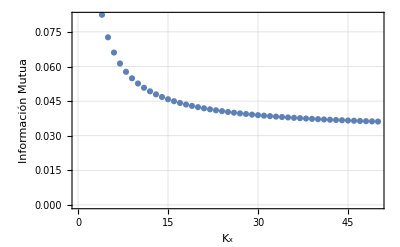

```mathematica
ListPlot[{Range[1,50],InformacionYXvariante }ᵀ, Frame->True, FrameStyle->Black, FrameLabel->{{"Información mutua",None}, {"K_x","Información mutua I(Y;X)"}}, GridLines->Automatic]

ListPlot[{Range[1,50],InformacionZXvariante }ᵀ, Frame->True, FrameStyle->Black, FrameLabel->{{"Información mutua",None}, {"K_x","Información mutua I(Z;X)"}}, GridLines->Automatic]

ListPlot[{Range[1,50],InformacionZYvariante }ᵀ, Frame->True, FrameStyle->Black, FrameLabel->{{"Información mutua",None}, {"K_x","Información Mutua I(Z;Y)"}}, GridLines->Automatic]

ListPlot[{Range[1,50],InformacionZXYvariante }ᵀ, Frame->True, FrameStyle->Black, FrameLabel->{{"Información Mutua",None}, {"K_x","Información Mutua I(Z;X,Y)"}}, GridLines->Automatic]
```